```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Import data thief of WD mass-density + WD mass-radius relations

```mathematica
WD=Import["/Users/NewUser/Documents/Qballs/WD.csv"];
WDrad=Import["/Users/NewUser/Documents/Qballs/WDradius.csv"];
WDreverse=Reverse/@WD;
Massreverse=Interpolation[WDreverse];
WDplot=Interpolation[WD];Radplot=Interpolation[WDrad];
```

#### Range of densities

```mathematica
{triggermass[0.85],triggermass[1.37]}
```

{0.00337513,0.0000124363}

```mathematica
{Massreverse[0.85],Massreverse[1.25],Massreverse[1.37]}
```

{7.1606,8.46005,9.50943}

```mathematica
{Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->7.16},Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->8.46},Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->9.5}}
```

{(7.20147×10^29)/Centimeter^3,(1.43688×10^31)/Centimeter^3,(1.57551×10^32)/Centimeter^3}

```mathematica
6*{(7.201468136264897*^29)/Centimeter^3,(1.4368817984738546*^31)/Centimeter^3,(1.5755095624615844*^32)/Centimeter^3}
```

{(4.32088×10^30)/Centimeter^3,(8.62129×10^31)/Centimeter^3,(9.45306×10^32)/Centimeter^3}

```mathematica
Convert[9.453057374769507*^32 Centimeter^-3(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]//N
```

7.56245 ElectronVolt^3 Mega^3

WD data

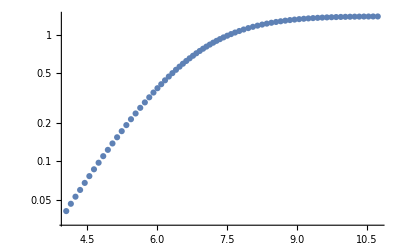

```mathematica
ListLogPlot[WD]
```

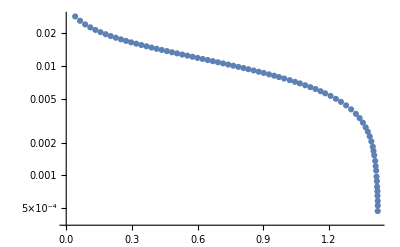

```mathematica
ListLogPlot[WDrad]
```

```mathematica
Convert[Radplot[1.25]SolarRadius,Kilo Meter]
```

3328.47 Kilo Meter

```mathematica
Convert[Radplot[0.85]SolarRadius,Kilo Meter]
```

6392.93 Kilo Meter

#### V_esc

```mathematica
Clear[vesc]
vesc[M_]:=Convert[Sqrt[2GravitationalConstant*M/Radplot[M]*SolarMass/SolarRadius] 1/SpeedOfLight,d]
```

```mathematica
vesc[1.25]
```

0.0305435

```mathematica
vesc[0.85]
```

0.0182875

#### λ_T as function of mass

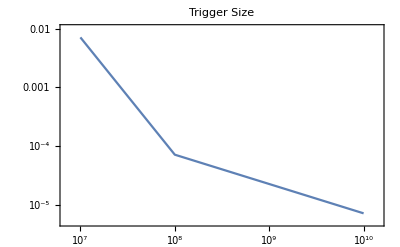

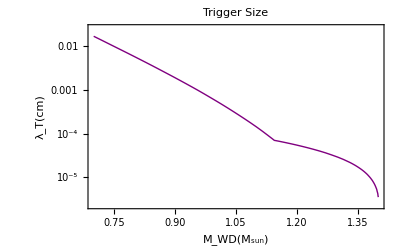

```mathematica
trigger[ρ_]:=If[ρ>10^8,10^-5*(ρ/(5*10^9))^(-1/2),1/(10000 √2)*(ρ/10^8)^-2]
triggermass=Interpolation[Table[{WDplot[logρ],trigger[10^logρ]},{logρ,5,10.6,0.01}]];
LogLogPlot[{trigger[ρ]},{ρ,10^10,10^7},PlotLabel->"Trigger Size",Frame->True]
LogPlot[triggermass[M],{M,0.7,1.4},PlotLabel->"Trigger Size",Frame->True,PlotStyle->{Thick,Purple},FrameLabel->{"M_WD(M_sun)","λ_T(cm)"},FrameStyle->Black]
```

#### E_boom (in GeV) as function of WD mass

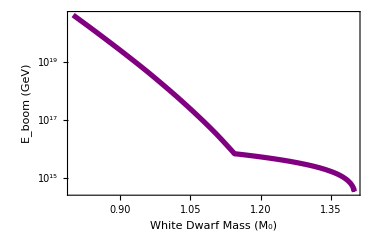

```mathematica
eboom[M_]:=Log10[Convert[(10^Massreverse[M]*Gram/Centimeter^3 SpeedOfLight^2)/(12 Giga ElectronVolt)*4 Pi/3(triggermass[M]Centimeter)^3*(Mega ElectronVolt)1/(Giga ElectronVolt),d]]
eboomdensity[ρ_]:=Log10[Convert[((ρ Gram)/Centimeter^3 SpeedOfLight^2)/(12 Giga ElectronVolt)*4 Pi/3(trigger[ρ]Centimeter)^3*(Mega ElectronVolt)1/(Giga ElectronVolt),d]]
eboomreverse[mdm_]:=Interpolation[Table[{eboom[M],M},{M,0.4,1.40,0.01}],InterpolationOrder->1][mdm]
XLabelEboom = {{0.2, "0.2"},{0.3, "0.3"},{0.4, "0.4"},{0.5, "0.5"}, {0.6, "0.6"},{0.7, "0.7"},  {0.8, "0.8"},{0.9, "0.9"}, {1.0, "1.0"},{1.1, "1.1"}, {1.2, "1.2"},{1.3, "1.3"}, {1.4, "1.4"}}; 
YLabelEboom = {{15, "10^15"}, {16, "10^16"},{17, "10^17"}, {18, "10^18"}, {19, "10^19"},  {20, "10^20"},{21, "10^21"},{22, "10^22"},{23, "10^23"}}; 
Eboom=Plot[eboom[M],{M,0.8,1.40},Frame->True,FrameTicks-> {{YLabelEboom,None},{Automatic,None}},FrameLabel->{"White Dwarf Mass (M_0)","E_boom (GeV)"},FrameStyle->Black,PlotStyle-> {Purple,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```

```mathematica
10^Massreverse[1.25]
```

2.88433×10^8

```mathematica
Massreverse[1.3]
```

```mathematica
10^8.76728248628087
```

5.85171×10^8

```mathematica
eboomdensity[10^-2 5.851705838284264*^8]
```

22.0039

```mathematica
WDplot[Log10[5*10^9]]
```

1.37959

```mathematica
Export["/Users/NewUser/Documents/Qballs/Eboom.pdf",Eboom];
```

```mathematica
eboom[1.4]
```

14.5278

```mathematica
eboom[1.25]
```

15.6102

```mathematica
eboom[0.85]
```

20.0373

```mathematica
eboomreverse[15.2]
```

1.35431

#### Model-dependent crust stopping calculation R_c~ 50 km, ρ_c~ 10^-2 ρ_interior)

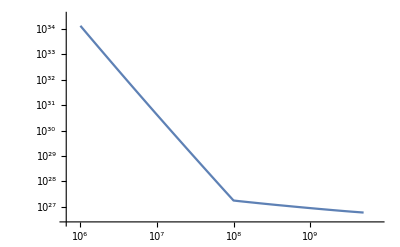

```mathematica
LogLogPlot[Convert[((Mega ElectronVolt)/vesc[WDplot[Log10[ρ]]]^2(trigger[ρ]*Centimeter)^2*ρ*10^-2 Gram/Centimeter^3*1/(10 Giga ElectronVolt)*SpeedOfLight^2(50Kilo Meter))1/(Giga ElectronVolt),d],{ρ,10^6,5*10^9}]
```

#### SN information

```mathematica
snrate=0.3/Century; 
whitedwarfdistribution[m_] := 1/(0.14 Sqrt[2 π])Exp[(-(m - 0.64)^2)/(2 (0.14)^2)];
integralcollision[logmdm_]:=Re[NIntegrate[vesc[x]^3 4 Pi/3(Radplot[x]*restrict)^3 10^10 whitedwarfdistribution[x],{x,(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85]),1.4}]]
unitlesscollision=Convert[snrate*((10^logmdm Giga ElectronVolt)/(0.4 (Giga ElectronVolt)/Centimeter^3))^2((10^-3 SpeedOfLight)^2)/(SpeedOfLight^3*SolarRadius^3),Centimeter^2] 1/Centimeter^2;
```

```mathematica
integraldecay[logmdm_]:=Re[NIntegrate[vesc[x] 4 Pi/3(Radplot[x]*restrict)^3 10^10 whitedwarfdistribution[x],{x,(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85]),1.4}]]
unitlessdecay=Convert[1/snrate (0.4(Giga ElectronVolt)/Centimeter^3)/(10^logmdm Giga ElectronVolt)(SpeedOfLight SolarRadius^3)/(10^-3 SpeedOfLight),Giga Year] 1/(Giga Year);
```

#### How much of the WD detector should we observe?

```mathematica
restrict=1/2;
```

#### Collision Constraints

```mathematica
σcollision=Γcollision ((ρdm/mdm)^2 (vesc/v)^3 v 4 Pi/3(Rwd*restrict)^3)^-1;
σobsRX=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
σobsNuStar=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
```

```mathematica
σobsRX/.logmdm->eboom[1.25]
```

3.07857×10^-23

```mathematica
σobsNuStar/.logmdm->eboom[1.25]
```

4.92571×10^-30

```mathematica
SNcollision=Plot[Log10[unitlesscollision 1/integralcollision[logmdm]],{logmdm,14.527763646029436,22},PlotStyle->{Green,Thick}];
```

```mathematica
eboomlimitcollision1=Plot[(100 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{-35,-10}];
eboomlimitcollision2=Plot[(100 Sign[x-(eboom[1.25]-Log10[10^-3])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Yellow}],PlotRange->{-35,-10}];
collisionlimitSN=Plot[( 100 Sign[x-14.527763646029436]),{x,14,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{-19.907340306203004,5}];
RXcollision=Plot[Log10[σobsRX],{logmdm,eboom[1.25],22},PlotStyle->{Blue,Thick}];
NuStarcollision=Plot[Log10[σobsNuStar],{logmdm,eboom[1.25],22},PlotStyle->{Gray,Thick}];
XLabelCollision={{14,"10^14"},{15,"10^15"},{16,"10^16"},{17,"10^17"},{18,"10^18"},{19,"10^19"},{20,"10^20"},{21,"10^21"}};
YLabelCollision={{-30,"10^-30"},{-25,"10^-25"},{-20,"10^-20"},{-15,"10^-15"}};
canvascollision=Plot[-100,{logmdm,14,21},Frame->True,FrameTicks->{{YLabelCollision,None},{XLabelCollision,None}},FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(DM - DM) (cm^2)"},PlotRange->{-32,-13},Axes->None];
canvascollisioneta=Plot[-100,{logmdm,15,21},Frame->True,FrameTicks->{{YLabelCollision,None},{XLabelCollision,None}},FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(DM - DM) (cm^2)"},PlotRange->{-24,-13},Axes->None];
```

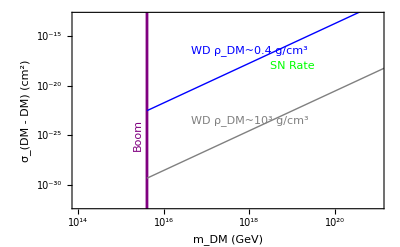

```mathematica
collisionobservation=Show[canvascollision,eboomlimitcollision1,RXcollision,(*SNcollision,*) NuStarcollision,Graphics[Inset[Style["WD ρ_DM~0.4 g/cm^3",Small,Blue,FontFamily->"Helvetica"],{18,-16.5},{0,0},10,{1,1/2}]],Graphics[Inset[Style["WD ρ_DM~10^3 g/cm^3",Small,Gray,FontFamily->"Helvetica"],{18,-23.5},{0,0},10,{1,1/2}]],Graphics[Inset[Style["SN Rate",Small,Green,FontFamily->"Helvetica"],{19,-18},{0,0},10,{1,1/3}]],Graphics[Inset[Style["Boom",Small,Purple,FontFamily->"Helvetica"],{15.4,-25},{0,0},10,{0,1}]]]
```

#### Decay Constraints

```mathematica
τdm=1/Γdecay(ρdm/mdm) (vesc/v)4 Pi/3(Rwd restrict)^3;
τobsRX=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
τobsNuStar=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
```

```mathematica
τobsRX/.logmdm->eboom[1.25]
```

3.15562×10^11

```mathematica
τobsNuStar/.logmdm->eboom[1.25]
```

7.88906×10^14

```mathematica
SNdecay=Plot[Log10[unitlessdecay integraldecay[logmdm]],{logmdm,14.527763646029436,22},PlotStyle->{Green,Thick}];
```

```mathematica
RXdecay=Plot[Log10[τobsRX],{logmdm,eboom[1.25],22},PlotStyle->{Blue,Thick}];
NuStardecay=Plot[Log10[τobsNuStar],{logmdm,eboom[1.25],22},PlotStyle->{Gray,Thick}];eboomlimitdecay1=Plot[(100 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{5,20}];
eboomlimitdecay2=Plot[(100 Sign[x-(eboom[1.25]-Log10[10^-3])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Yellow}],PlotRange->{5,20}];
decaylimitSN=Plot[(100 Sign[x-14.527763646029436]),{x,14,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{-10,7.2644500547759}];
YLabelDecay={{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"},{14,"10^14"},{16,"10^16"}};
canvasdecay=Plot[-100,{logmdm,14,21},Frame->True,FrameTicks->{{YLabelDecay,None},{XLabelCollision,None}},FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "τ_DM (Gyr)"},PlotRange->{5,16},Axes->None];
canvasdecayeta=Plot[-100,{logmdm,15,21},Frame->True,FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "τ_DM (Gyr)"},PlotRange->{5,12},Axes->None];
```

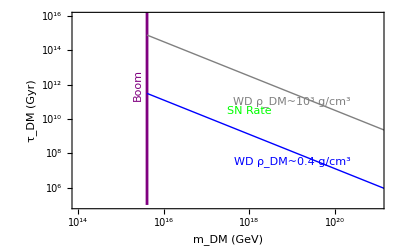

```mathematica
decayobservation=Show[canvasdecay,eboomlimitdecay1,RXdecay,NuStardecay,(*SNdecay,*)Graphics[Inset[Style["WD ρ_DM~0.4 g/cm^3",Small,Blue,FontFamily->"Helvetica"],{19,7.5},{0,0},10,{1,-1/2.5}]],Graphics[Inset[Style["WD ρ_DM~10^3 g/cm^3",Small,Gray,FontFamily->"Helvetica"],{19,11},{0,0},10,{1,-1/2.5}]],Graphics[Inset[Style["SN Rate",Small,Green,FontFamily->"Helvetica"],{18,10.5},{0,0},10,{1,-1/10}]],Graphics[Inset[Style["Boom",Small,Purple,FontFamily->"Helvetica"],{15.4,12},{0,0},10,{0,1}]]]
```

#### Transit Constraints for L_0<λ_T: ϵ = TeV

```mathematica
transitreverse=Interpolation[Table[{Log10[10^-3/ϵ*triggermass[Mwd]^2],Mwd}/.{ϵ->10^3},{Mwd,0.4,1.4,0.01}],InterpolationOrder->1];
integraltransit[logσ_]:=Re[NIntegrate[vesc[x]^2 Pi (restrict Radplot[x])^2 10^10 whitedwarfdistribution[x],{x,(If[transitreverse[logσ]≥0.85,transitreverse[logσ], 0.85]),1.40}]]
transitfun=Convert[(ρdm/mdm)π Rwd^2(vesc/v)^2 v/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},1/Century];
unitlesstransit=Convert[1/snrate*0.4 (Giga ElectronVolt)/Centimeter^3*SpeedOfLight^2/(10^-3 SpeedOfLight)*SolarRadius^2,Giga ElectronVolt] 1/(Giga ElectronVolt);
```

```mathematica
Log10[unitlesstransit*integraltransit[-10.94]]
```

46.0239

```mathematica
transitSN=Interpolation[Table[{Log10[unitlesstransit*integraltransit[logσ]],logσ},{logσ,-16.9,-10.94,0.01}]];
```

```mathematica
crust=Log10[Convert[vesc[1.25]^2/(10^30 Centimeter^-3*50Kilo Meter)10^mdm/ϵ,Centimeter^2] 1/Centimeter^2];
transitboom=Log10[10^-3/ϵ*triggermass[1.25]^2];
crustplotTeV=Plot[crust/.ϵ->10^3,{mdm,25,50},PlotStyle->{Dashed,Black,Thick}];
photontransitTeV=Plot[transitboom/.ϵ->10^3,{mdm,24,52},PlotStyle->{Thick,Purple}];
transitSNTeV=Plot[transitSN[logmdm],{logmdm,36.680724877647286,46.023911281165695},PlotStyle->{Green,Thick}];
fluxlimitRX=Plot[( 100 Sign[x-44]),{x,24,50},ExclusionsStyle->Directive[{Thickness[.005],Blue}],PlotRange->{-20,5}];
fluxlimitNuStar=Plot[( 100 Sign[x-48]),{x,24,50},ExclusionsStyle->Directive[{Thickness[.005],Gray}],PlotRange->{-20,5}];
fluxlimitSN=Plot[( 100 Sign[x-46.023911281165695]),{x,24,50},ExclusionsStyle->Directive[{Thickness[.0059],Green}],PlotRange->{-10.94,5}];
tailSN=Plot[-16.9,{x,24,36.680724877647286},PlotStyle->{Green,Thick}];
YLabelTransit={{-20,"10^-20"},{-15,"10^-15"},{-10,"10^-10"},{-5,"10^-5"},{0,"1"},{5,"10^5"}};
XLabelTransit={{25,"10^25"},{30,"10^30"},{35,"10^35"},{40,"10^40"},{45,"10^45"},{50,"10^50"}};
canvastransit=Plot[-100,{x,25,50},Frame->True,FrameTicks->{{YLabelTransit,None},{XLabelTransit,None}},FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(photon, TeV) (cm^2)"},PlotRange->{-20,5},Axes->None];
crustplotPeV=Plot[crust/.ϵ->10^6,{mdm,25,50},PlotStyle->{Dashed,Red,Thick}];
photontransitPeV=Plot[transitboom/.ϵ->10^6,{mdm,25,50},PlotStyle->{Thick,Purple}];
```

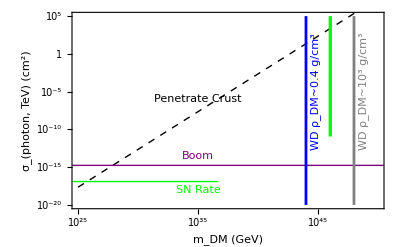

```mathematica
transitobservation=Show[canvastransit,crustplotTeV,photontransitTeV,fluxlimitRX,fluxlimitNuStar,fluxlimitSN,tailSN,transitSNTeV,Graphics[Inset[Style["Boom",Small,Purple,FontFamily->"Helvetica"],{35,-13.5},{0,0},4,{1,0}]],
Graphics[Inset[Style["SN Rate",Small,Green,FontFamily->"Helvetica"],{35,-18},{0,0},4,{1,0}]],Graphics[Inset[Style["WD ρ_DM~10^3 g/cm^3",Small,Gray,FontFamily->"Helvetica"],{48.8,-5},{0,0},12,{0,1}]],Graphics[Inset[Style["WD ρ_DM~0.4 g/cm^3",Small,Blue,FontFamily->"Helvetica"],{44.8,-5},{0,0},12,{0,1}]],Graphics[Inset[Style["Penetrate Crust",Small,FontFamily->"Helvetica"],{35,-6},{0,0},10,{1,3/5}]]]
```

#### Competing Constraints

```mathematica
σHalo=Convert[Barn/(ElectronVolt Giga)mdm Giga ElectronVolt/.mdm->10^logmdm,Centimeter^2] 1/Centimeter^2;
σCMB=Convert[(1.0006922855944562*^-7 Barn)/(ElectronVolt Giga)mdm Giga ElectronVolt/.mdm->10^logmdm,Centimeter^2] 1/Centimeter^2;
σCR=Convert[1/(5 Year)*(((0.3 Giga ElectronVolt)/Centimeter^3 1/(mdm Giga ElectronVolt))^2 10^-3 SpeedOfLight*(50 Kilo Meter)^2(50 Kilo Parsec))^-1,Centimeter^2] 1/Centimeter^2/.mdm->10^logmdm;
τCR=Convert[(0.3 Giga ElectronVolt)/Centimeter^3*1/(mdm Giga ElectronVolt)*(50 Kilo Meter)^2(50 Kilo Parsec)*5 Year,Giga Year] 1/(Giga Year)/.mdm->10^logmdm;
τcosmo=10^2 Giga Year*1/(Giga Year);
```

#### Q-ball boom

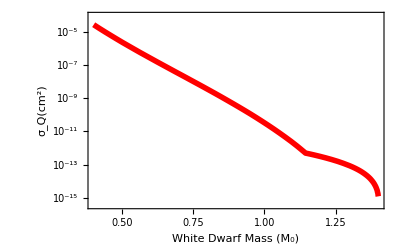

```mathematica
LogPlot[1/10^4*(triggermass[M])^2,{M,0.4,1.4},Frame->True,FrameLabel->{"White Dwarf Mass (M_0)","σ_Q(cm^2)"},FrameStyle->Black,PlotStyle-> {Red,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```